```mathematica
<<NDSolve`FEM`
nb=NotebookOpen[StringJoin[NotebookDirectory[],"Base2D.nb"]];
NotebookEvaluate[nb];
NotebookClose[nb];
```

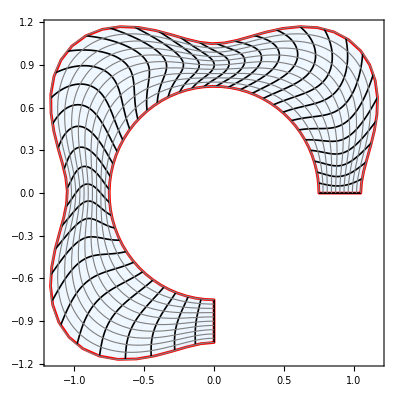

```mathematica
a=1+.2Cos[ 2(v-1/2)]^2;
rg=3/4;
α={Cos[rg 2Pi s],Sin[rg 2Pi s]};
v1=-1/4 +.2Cos[3 2Pi s];
v2=1/4;
p=FrenetChannel2D[α,v1,v2]/.s->s^a;
pG=ParametricChannelPlot2D[p];
Show[pG,AspectRatio->1,Axes->False]
```

# Harmonic coordinate for 2D channels

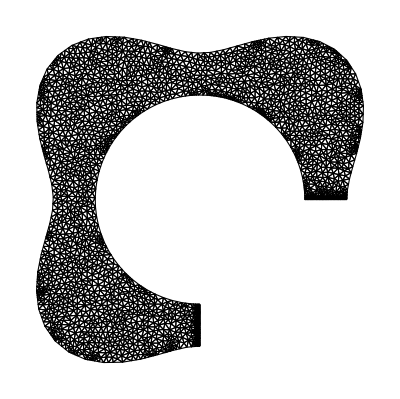

-Graphics3D-

```mathematica
ch=ParametricRegion[p,{{s,0,1},{v,0,1}}];
box={{-1.5,1.5},{-1.5,1.5}};
mesh=ToElementMesh[ch,box,MaxCellMeasure->.001];
mesh["Wireframe"]
lft=((y==0) && (x>0));
rgt=((x==0)&& (y<0));
ϕ=NDSolveValue[{∇_{x,y}^2 ψ[x,y] ==0,
DirichletCondition[ψ[x, y] == 0.0,lft],
DirichletCondition[ψ[x, y] == 1.0,rgt]}, ψ, {x, y} ∈ mesh,InterpolationOrder->All];
Plot3D[ϕ[x,y],{x,y}∈mesh,Mesh->None]
ϕx=Derivative[1,0][ϕ];
ϕy=Derivative[0,1][ϕ];
gϕ[x_,y_]:={ϕx[x,y],ϕy[x,y]};
```

Level curves OK!

Level curves OK!

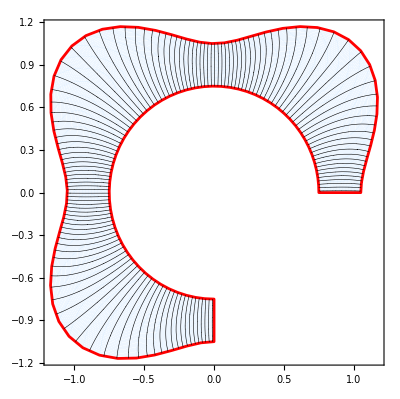

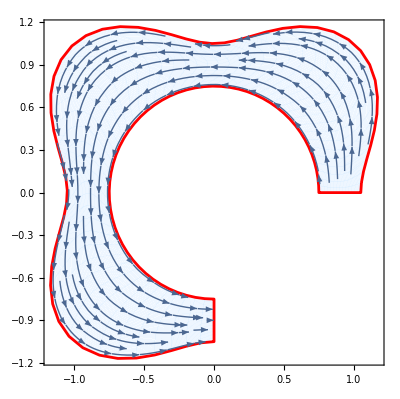

```mathematica
{us, dus, Sus}=getLevelSets[ϕ,mesh,0,1,.008];
uMin=Min[us];
uMax=Max[us];
uDomain = {u,uMin,uMax};

If[Length[Sus]==Length[us], Print["Level curves OK!"], Print["Faulty Level curves, Correcting!"]];
Sus=Select[Sus,Length[#]>2&]; (* Removing Faulty Curves *)
If[Length[Sus]==Length[us], Print["Level curves OK!"], Print["Faulty Level curves, Check criteria!"]];

lG=ListPlot[Sus,Joined->True,PlotStyle->Directive[Thickness[.001],Black]];
sG=StreamPlot[gϕ[x,y],{x,y}∈mesh,StreamPoints->Fine];
chG=ParametricPlot[p,{s,0,1},{v,0,1},PlotStyle->LightBlue,
BoundaryStyle->Directive[Red,Thickness[.005]]];
Show[chG,lG,Axes->False]
Show[chG,sG,Axes->False]
```